```mathematica
Quit
```

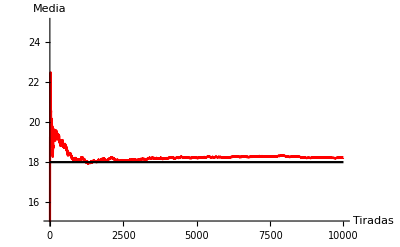

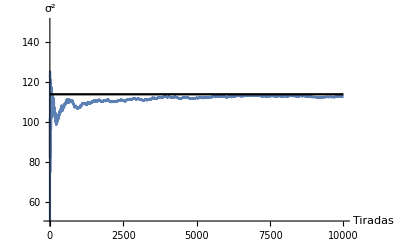

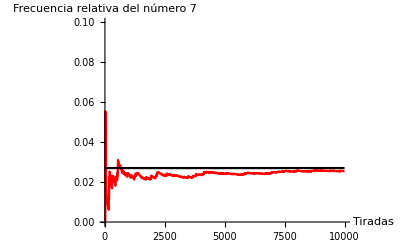

```mathematica
kmax=10^4;

m=1/37 ∑_(k=0)^36 k; (*Esto sería el promedio de la suma de 0 a 36*)
s= ∑_(k=0)^36 (k-m)^2 1/37;
tiradas={IntegerPart[37 RandomReal[]]};
Do[ (*Ciclo de repetición k (con 1=< k =<kmax)*)
{tiradas=Append[tiradas,IntegerPart[37 RandomReal[]]], (*Acá se le agrega al listado "tiradas" un entero en cada repetición*)
media[k]=Mean[tiradas],(*Acá se va calculando el promedio de tiradas y se guarda en la variable "media"*)
var[k]=Variance[tiradas], (*Acá se va calculando la varianza de tiradas y se guarda en la variable "var"*)
fr[k]=Count[tiradas,7]/k}, (*Acá se va calculando la frecuencia relativa del número 7 y se guarda en la variable "fr"*)
{k,1,kmax}] (*Parámetros del DO*)

(*Acá se crean las listas de la media, la varianza y la frecuencia relativa del número 7*)
tablamedia=Table[{k,media[k]},{k,1,kmax}];
tablavar=Table[{k,var[k]},{k,1,kmax}];
tablafr=Table[{k,fr[k]},{k,1,kmax}];

gm=Plot[m,{x,1,kmax}, PlotStyle-> Black];(*Gráfica de la media "a priori"*)
l2=ListPlot[tablamedia,Joined-> True,PlotStyle->Red, PlotRange->{15,25}, AxesLabel->{"Tiradas", "Media"}];
Show[l2,gm]  (*  cada vez que se ejecute cambiar el nombre al grafico  y su color*)

gs=Plot[s,{x,1,kmax}, PlotStyle-> Black]; (*Esta es la gráfica de la constante "s" varianza*)
v1=ListPlot[tablavar,Joined-> True, AxesLabel->{"Tiradas", "σ^2"},PlotRange->{50,150}]; (*Esta es la gráfica de la varianza observada*)
Show[v1,gs](*Esto es la union de gs y v1 para ser mostradas*)


gf=Plot[1/37,{x,1,kmax}, PlotStyle-> Black]; (*Gráfica de la constante 1/37, probabilidad de ocurrencia del 7*)

f1=ListPlot[tablafr,Joined-> True,PlotStyle->Red, PlotRange->{0,.1}, AxesLabel->{"Tiradas", "Frecuencia relativa del número  7"}];
Show[f1,gf]
```